## ex 1 pp 111

```mathematica
Clear[θ]
circle[θ_]:=(1+E^(I*θ))
```

```mathematica
angles=Range[0,2Pi,Pi/4]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

```mathematica
circle[angles]
```

{2,1+ⅇ^((ⅈ π)/4),1+ⅈ,1+ⅇ^((3 ⅈ π)/4),0,1+ⅇ^(-(3 ⅈ π)/4),1-ⅈ,1+ⅇ^(-(ⅈ π)/4),2}

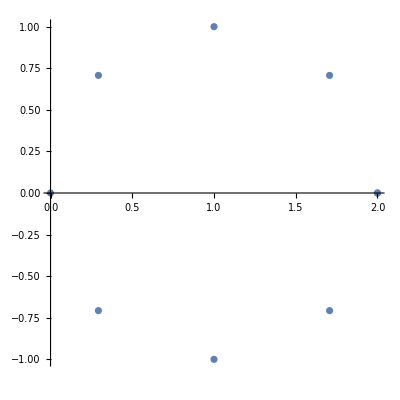

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{2,1+ⅇ^((ⅈ π)/4),1+ⅈ,1+ⅇ^((3 ⅈ π)/4),0,1+ⅇ^(-(3 ⅈ π)/4),1-ⅈ,1+ⅇ^(-(ⅈ π)/4),2},AspectRatio->1]
```

```mathematica
circle[angles]^2
```

{4,(1+ⅇ^((ⅈ π)/4))^2,2 ⅈ,(1+ⅇ^((3 ⅈ π)/4))^2,0,(1+ⅇ^(-(3 ⅈ π)/4))^2,-2 ⅈ,(1+ⅇ^(-(ⅈ π)/4))^2,4}

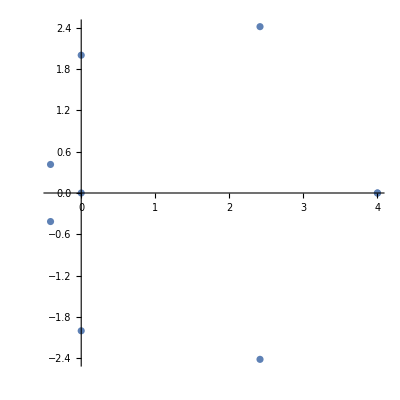

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{4,(1+ⅇ^((ⅈ π)/4))^2,2 ⅈ,(1+ⅇ^((3 ⅈ π)/4))^2,0,(1+ⅇ^(-(3 ⅈ π)/4))^2,-2 ⅈ,(1+ⅇ^(-(ⅈ π)/4))^2,4},AspectRatio->1]
```

```mathematica
numbers=Range[1,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
test[x_]:=(1/x)
```

```mathematica
N[Total[test[Range[1,10000000]]]]
```

16.6953